## Common definitions

```mathematica
headerFolder="F:\\MathematicaWork\\FreeFermion\\Result\\";
lat={4,4,4,4};

testgmStr1={"","γ_1","γ_2","γ_3","γ_4","γ_5","σ_12","σ_13","σ_14","σ_23","σ_24","σ_34","γ_5γ_1","γ_5γ_2","γ_5γ_3","γ_5γ_4"};
testgmStr2={"μ","μ_1","μ_2","μ_3","μ_4","μ_5","μ_12","μ_13","μ_14","μ_23","μ_24","μ_34","μ_51","μ_52","μ_53","μ_54"};
```

```mathematica
investigateGamma={
gmu,
gm1,
gm2,
gm3,
gm4,
gm5,
I/2(gm1.gm2-gm2.gm1),
I/2(gm1.gm3-gm3.gm1),
I/2(gm1.gm4-gm4.gm1),
I/2(gm2.gm3-gm3.gm2),
I/2(gm2.gm4-gm4.gm2),
I/2(gm3.gm4-gm4.gm3),
gm5.gm1,
gm5.gm2,
gm5.gm3,
gm5.gm4
};

gammaMatrixTerms=Table[diagnalTerm[1.0,lat,investigateGamma[[k]]],{k,1,Length[investigateGamma]}];
```

```mathematica
testList=Table[-0.2+0.01*n,{n,0,40}];
```

S_F=ψ̄ D ψ, D=D_0-μ Γ
测量的是<-(∂S_F)/(∂μ)> =<ψ̄ Γ ψ> =-tr[Γ D^-1]=tr[(∂D)/(∂μ) D^-1]

## Naive discretization

## D0 term

```mathematica
d0naive=naiveDNum[lat,0,torusBound];
doperatorWithCond[coef_,k_]:=d0naive-coef gammaMatrixTerms[[k]];
d0naiveinv=Inverse[d0naive];
```

## gamma term

```mathematica
allres={};
Dynamic[prog];
prog=0;
ProgressIndicator[Dynamic[prog]]
For[m=1,m<=Length[investigateGamma],m++,
test1=Table[{testList[[q]],-Tr[gammaMatrixTerms[[m]].Inverse[doperatorWithCond[testList[[q]],m]]]},{q,1,Length[testList]}];
prog=prog+1/(2Length[investigateGamma]);
test2=Table[{testList[[q]],-Im[Tr[gammaMatrixTerms[[m]].Inverse[doperatorWithCond[testList[[q]] I,m]]]]},{q,1,Length[testList]}];
prog=prog+1/(2Length[investigateGamma]);
AppendTo[allres,{test1,test2}];
];
```

```mathematica
derivatesNaive=Table[Tr[gammaMatrixTerms[[k]].d0naiveinv.gammaMatrixTerms[[k]].d0naiveinv],{k,1,Length[investigateGamma]}];
```

## Result presents

```mathematica
Export[headerFolder<>"naiveCond.csv",allres];
```

## Graphics

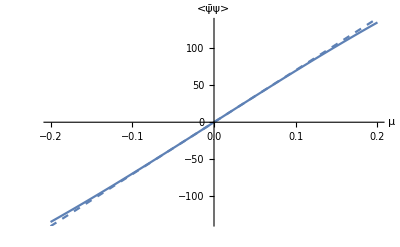
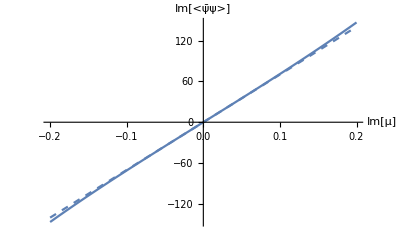

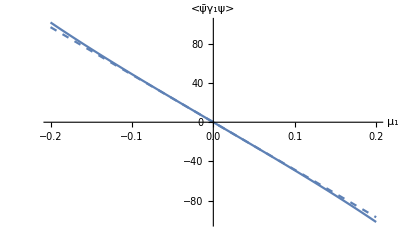
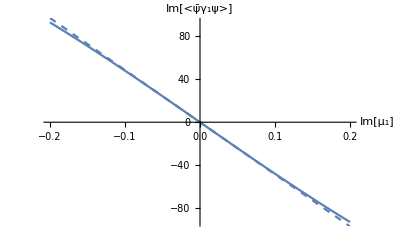

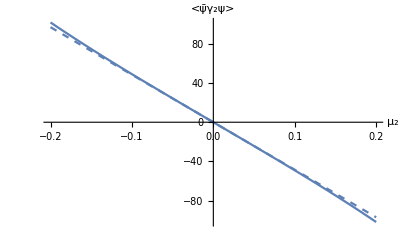
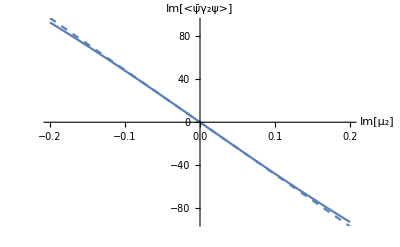

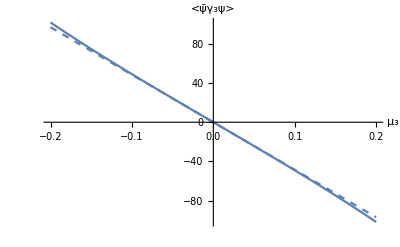
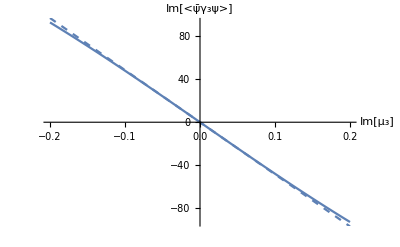

```mathematica
For[m=1,m<=Length[investigateGamma],m++,
pic1=Show[ListLinePlot[allres[[m]][[1]],AxesLabel->{testgmStr2[[m]],"<ψ̄"<>testgmStr1[[m]]<>"ψ>"}],Plot[-derivatesNaive[[m]]x ,{x,-0.2,0.2},PlotStyle->Dashed]];
pic2=Show[ListLinePlot[allres[[m]][[2]],PlotRange->All,AxesLabel->{"Im["<>testgmStr2[[m]]<>"]","Im[<ψ̄"<>testgmStr1[[m]]<>"ψ>]"}],Plot[-derivatesNaive[[m]]x ,{x,-0.2,0.2},PlotStyle->Dashed]];
Print[{pic1,pic2}];
]
```

## Wilson Dirac discretization

## D0 term

```mathematica
d0wilson=wilsonDiracDNum[lat,0.125,torusBound];
doperatorWithCondWilson[coef_,k_]:=d0wilson-coef gammaMatrixTerms[[k]];
```

## gamma term

```mathematica
allresWilson={};
Dynamic[prog];
prog=0;
ProgressIndicator[Dynamic[prog]]
For[m=1,m<=Length[investigateGamma],m++,
test1=Table[{testList[[q]],-Tr[gammaMatrixTerms[[m]].Inverse[doperatorWithCondWilson[testList[[q]],m]]]},{q,1,Length[testList]}];prog=prog+1/(2Length[investigateGamma]);
test2=Table[{testList[[q]],-Im[Tr[gammaMatrixTerms[[m]].Inverse[doperatorWithCondWilson[testList[[q]] I,m]]]]},{q,1,Length[testList]}];
prog=prog+1/(2Length[investigateGamma]);
AppendTo[allresWilson,{test1,test2}];
];
```

```mathematica
derivatesWilson=4 4 4 4 Table[Tr[investigateGamma[[k]].investigateGamma[[k]]],{k,1,Length[investigateGamma]}];
```

## Result presents

```mathematica
Export[headerFolder<>"wilsonCond.csv",allresWilson];
```

## Graphics

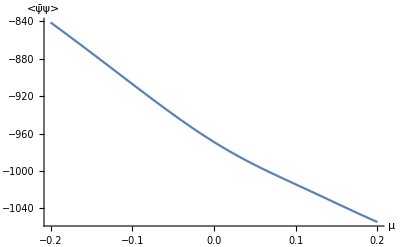
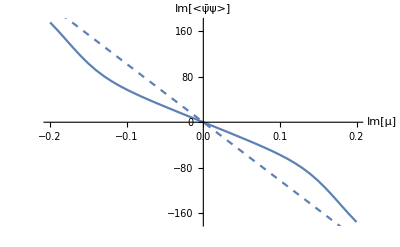

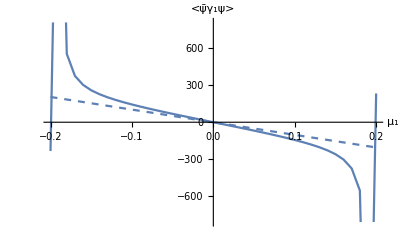
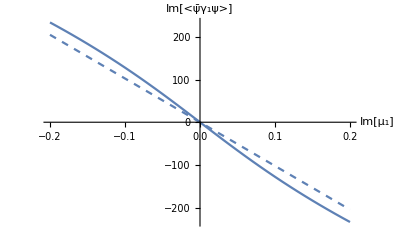

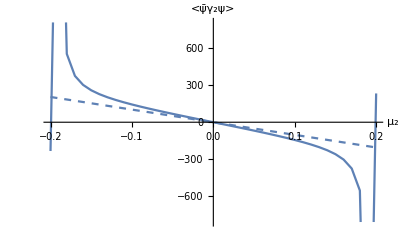
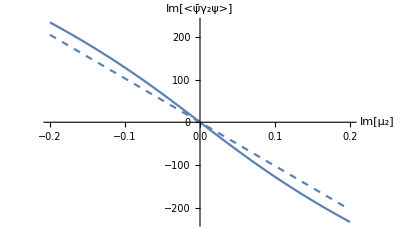

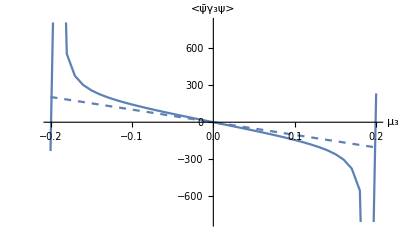
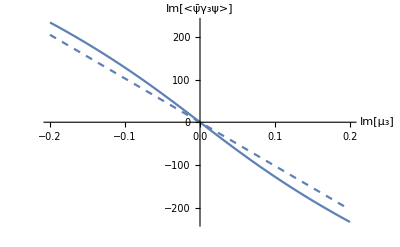

```mathematica
For[m=1,m<=Length[investigateGamma],m++,
pic1=Show[ListLinePlot[allresWilson[[m]][[1]],AxesLabel->{testgmStr2[[m]],"<ψ̄"<>testgmStr1[[m]]<>"ψ>"}],Plot[-derivatesWilson[[m]]x ,{x,-0.2,0.2},PlotStyle->Dashed]];
pic2=Show[ListLinePlot[allresWilson[[m]][[2]],PlotRange->All,AxesLabel->{"Im["<>testgmStr2[[m]]<>"]","Im[<ψ̄"<>testgmStr1[[m]]<>"ψ>]"}],Plot[-derivatesWilson[[m]]x ,{x,-0.2,0.2},PlotStyle->Dashed]];
Print[{pic1,pic2}];
]
```

## Test

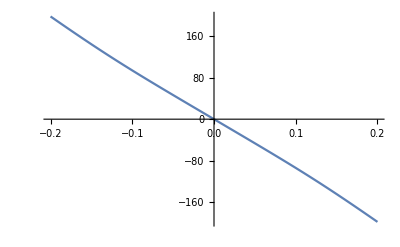

```mathematica
m=5;
ListLinePlot[Table[{testList[[q]],-Tr[gammaMatrixTerms[[m]].Inverse[doperatorWithCondWilson[testList[[q]],m]]]},{q,1,Length[testList]}]]
```

## Staggered discretization

```mathematica
stGammaI=2.0 diagnalTermStaggered[1.0,lat];
stGamma1=2.0 staggeredGammaNum[lat,0,torusBound];
stGamma2=2.0 staggeredGammaNum[lat,1,torusBound];
stGamma3=2.0 staggeredGammaNum[lat,2,torusBound];
stGamma4=2.0 staggeredGammaNum[lat,3,torusBound];
stGamma5=2.0 staggeredGamma5Num[lat,torusBound];
stSigma12=2.0 staggeredSigmaNum[lat,0,1,torusBound];
stSigma13=2.0 staggeredSigmaNum[lat,0,2,torusBound];
stSigma14=2.0 staggeredSigmaNum[lat,0,3,torusBound];
stSigma23=2.0 staggeredSigmaNum[lat,1,2,torusBound];
stSigma24=2.0 staggeredSigmaNum[lat,1,3,torusBound];
stSigma34=2.0 staggeredSigmaNum[lat,2,3,torusBound];
stGamma51=2.0 staggeredGamma5INum[lat,1,torusBound];
stGamma52=2.0 staggeredGamma5INum[lat,2,torusBound];
stGamma53=2.0 staggeredGamma5INum[lat,3,torusBound];
stGamma54=2.0 staggeredGamma5INum[lat,4,torusBound];

investigateGammaSt={
stGammaI,stGamma1, stGamma2, stGamma3, stGamma4, stGamma5,
stSigma12,stSigma13,stSigma14, stSigma23,stSigma24,stSigma34, 
stGamma51,stGamma52,stGamma53,stGamma54};
```

## D0 term

```mathematica
d0staggered=staggeredDiracDNum[lat,0,torusBound];
doperatorWithCondStaggered[coef_,k_]:=d0staggered-coef investigateGammaSt[[k]];
```

## gamma term

```mathematica
allresStaggered={};
Dynamic[prog];
prog=0;
ProgressIndicator[Dynamic[prog]]
For[m=1,m<=Length[investigateGammaSt],m++,
test1=Table[{testList[[q]],-Tr[investigateGammaSt[[m]].Inverse[doperatorWithCondStaggered[testList[[q]],m]]]},{q,1,Length[testList]}];prog=prog+1/(2Length[investigateGammaSt]);
test2=Table[{testList[[q]],-Im[Tr[investigateGammaSt[[m]].Inverse[doperatorWithCondStaggered[testList[[q]] I,m]]]]},{q,1,Length[testList]}];
prog=prog+1/(2Length[investigateGammaSt]);
AppendTo[allresStaggered,{test1,test2}];
];
```

## Result presents

```mathematica
Export[headerFolder<>"staggeredCond.csv",allresStaggered];
```

## Graphics

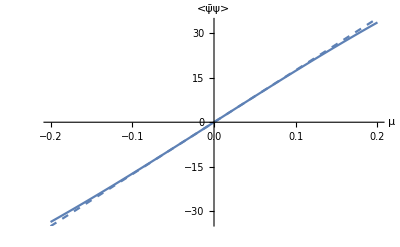
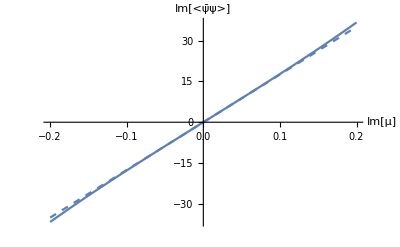

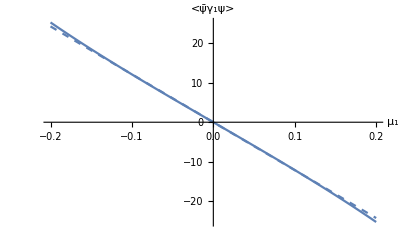
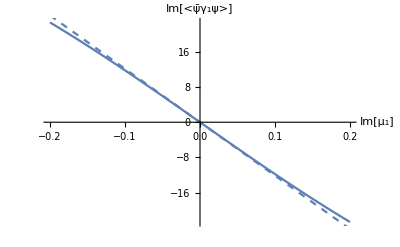

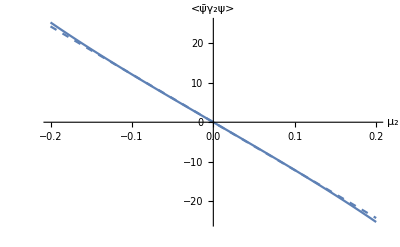
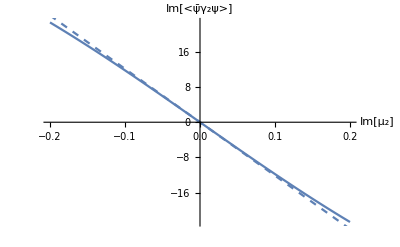

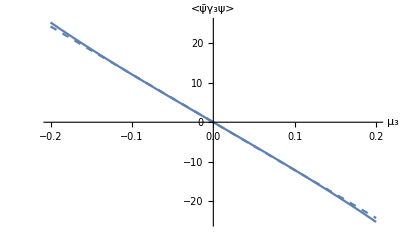
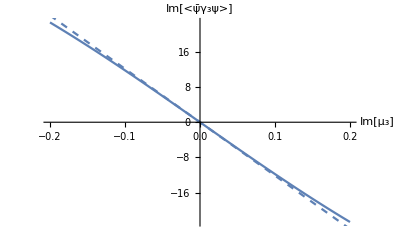

```mathematica
For[m=1,m<=Length[investigateGammaSt],m++,
pic1=Show[ListLinePlot[allresStaggered[[m]][[1]],AxesLabel->{testgmStr2[[m]],"<ψ̄"<>testgmStr1[[m]]<>"ψ>"}],Plot[-1/4 derivatesNaive[[m]]x ,{x,-0.2,0.2},PlotStyle->Dashed]];
pic2=Show[ListLinePlot[allresStaggered[[m]][[2]],PlotRange->All,AxesLabel->{"Im["<>testgmStr2[[m]]<>"]","Im[<ψ̄"<>testgmStr1[[m]]<>"ψ>]"}],Plot[-1/4 derivatesNaive[[m]]x ,{x,-0.2,0.2},PlotStyle->Dashed]];
Print[{pic1,pic2}];
]
```